```mathematica
R[t_]:=Subscript[R, I]+(2.02 Subscript[E, SN]/Subscript[p, 0])^(1/5)(t-ti)^(2/5);
D[R[t],t]
```

(0.460395 (ⅇ_SN/p_0)^(1/5))/(t-ti)^(3/5)

```mathematica
R2[t_,E_,p_,ti_]:=63072000000000000+(2 E/p)^(1/5)(t-ti)^(2/5);
R2[400*365*24*60*60*3,10^51,1.66*10^-24,400*365*24*60*60]
R3[t_,E_,p_,ti_]:=(0.4603946467498631 (E/p)^(1/5))/(t-ti)^(3/5)
R3[400*365*24*60*60+1,10^51,1.66*10^-24,400*365*24*60*60]
```

1.50925×10^19

4.16015×10^14

```mathematica
Plot[{R2[t,0.5*10^44,0.0167*10^-21,400*365*24*60*60],R2[t,10^44,1.674*10^-21,400*365*24*60*60],R2[t,2*10^44,167.34*10^-21,400*365*24*60*60]},{t,400*365*24*60*60*1,400*365*24*60*60*10}]
```

-Graphics-

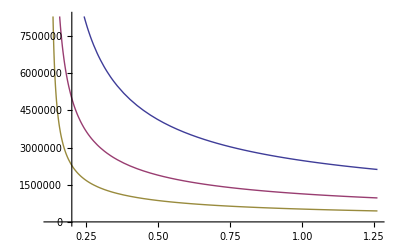

```mathematica
Plot[{R3[t,0.5*10^44,0.0167*10^-21,400*365*24*60*60],R3[t,10^44,1.674*10^-21,400*365*24*60*60],R3[t,2*10^44,167.34*10^-21,400*365*24*60*60]},{t,400*365*24*60*60*1,400*365*24*60*60*10}]
```

```mathematica
R2[2*10^10,{0.5*10^44,1*10^44,2*10^44},0.0167*10^-21,400*365*24*60*60]
R2[2*10^10,{0.5*10^44,1*10^44,2*10^44},1.674*10^-21,400*365*24*60*60]
R2[2*10^10,{0.5*10^44,1*10^44,2*10^44},167.37*10^-21,400*365*24*60*60]
```

{2.63894×10^17,2.93756×10^17,3.28058×10^17}

{1.42982×10^17,1.54865×10^17,1.68514×10^17}

{9.4886×10^16,9.96167×10^16,1.05051×10^17}

```mathematica
R2[4*10^10,{0.5*10^44,1*10^44,2*10^44},0.0167*10^-21,400*365*24*60*60]
R2[4*10^10,{0.5*10^44,1*10^44,2*10^44},1.674*10^-21,400*365*24*60*60]
R2[4*10^10,{0.5*10^44,1*10^44,2*10^44},167.37*10^-21,400*365*24*60*60]
```

{4.0228×10^17,4.52719×10^17,5.10659×10^17}

{1.98048×10^17,2.18119×10^17,2.41174×10^17}

{1.16809×10^17,1.248×10^17,1.33978×10^17}

```mathematica
R2[6*10^10,{0.5*10^44,1*10^44,2*10^44},0.0167*10^-21,400*365*24*60*60]
R2[6*10^10,{0.5*10^44,1*10^44,2*10^44},1.674*10^-21,400*365*24*60*60]
R2[6*10^10,{0.5*10^44,1*10^44,2*10^44},167.37*10^-21,400*365*24*60*60]
```

{4.85464×10^17,5.48273×10^17,6.20421×10^17}

{2.31149×10^17,2.56141×10^17,2.84851×10^17}

{1.29987×10^17,1.39937×10^17,1.51367×10^17}

```mathematica
R2[8*10^10,{0.5*10^44,1*10^44,2*10^44},0.0167*10^-21,400*365*24*60*60]
R2[8*10^10,{0.5*10^44,1*10^44,2*10^44},1.674*10^-21,400*365*24*60*60]
R2[8*10^10,{0.5*10^44,1*10^44,2*10^44},167.37*10^-21,400*365*24*60*60]
```

{5.49349×10^17,6.21657×10^17,7.04718×10^17}

{2.5657×10^17,2.85342×10^17,3.18394×10^17}

{1.40108×10^17,1.51563×10^17,1.64721×10^17}

```mathematica
R2[10*10^10,{0.5*10^44,1*10^44,2*10^44},0.0167*10^-21,400*365*24*60*60]
R2[10*10^10,{0.5*10^44,1*10^44,2*10^44},1.674*10^-21,400*365*24*60*60]
R2[10*10^10,{0.5*10^44,1*10^44,2*10^44},167.37*10^-21,400*365*24*60*60]
```